```mathematica
By Le Chen.
Crated on Tue 31 May 2022 06:06:03 PM CDT
```

```mathematica
Integrate[1/(2π)√(2-ξ) Cos[ x ξ],{ξ,0,2},Assumptions->x>0]//FullSimplify
```

(-Cos[2 x] FresnelS[(2 √x)/(√π)]+FresnelC[(2 √x)/(√π)] Sin[2 x])/(2 √(2 π) x^(3/2))

```mathematica
Limit[(-Cos[2 x] FresnelS[(2 √x)/(√π)]+FresnelC[(2 √x)/(√π)] Sin[2 x])/(2 √(2 π) x^(3/2)),x->0]
```

```mathematica
(2 √2)/(3 π)//N
```

0.300105

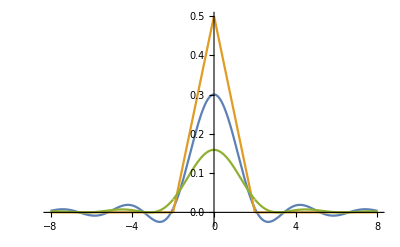

```mathematica
Plot[{(-Cos[2 x] FresnelS[(2 √x)/(√π)]+FresnelC[(2 √x)/(√π)] Sin[2 x])/(2 √(2 π) x^(3/2)),1/4 Max[2-Abs[x],0],Sin[x]^2/(2π x^2)},{x,-8,8},PlotRange->Full]
```

```mathematica
Data=Table[{x,(-Cos[2 x] FresnelS[(2 √Abs[x])/(√π)]+FresnelC[(2 √Abs[x])/(√π)] Sin[2 Abs[x]])/(2 √(2 π) Abs[x]^(3/2))},{x,-8.001,8.001,0.1}];

Export["InverseFourier.csv",PrependTo[Data,{x,y}],"CSV"]
```

InverseFourier.csv

```mathematica
Data=Table[{x,Sin[x]^2/(2π x^2)},{x,-8.001,8.001,0.1}];

Export["Sincx.csv",PrependTo[Data,{x,y}],"CSV"]
```

Sincx.csv

```mathematica
1/(2π)//N
```

0.159155